## ρ 介子

### 零宽度基态

#### 确定上截断。

```mathematica
s0=1.5;
a[M2_]:=(4π)/9 1/Log[M2/Λ^2]
cont[M2_,up_]:=∫_s0^up 3/2(1+a[s]/π)E^(-s/M2)ⅆs//N
Timing[
Table[cont[M2,up],{M2,0.8,0.9,0.1},{up,9,13}]
]
```

{7.191,{{0.18401,0.184021,0.184025,0.184026,0.184026},{0.254921,0.254962,0.254975,0.25498,0.254981}}}

#### 求出共振态贡献。

{15.007,Null}

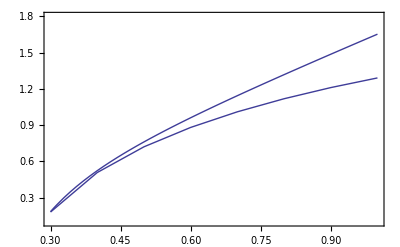

```mathematica
Clear[a, pts, plotsub, plotfull, f1, cont, contsubtract, s0]
Λ=0.1;s0=1.5; up=13;
min =0.3; max=1.2;
a[M2_]:=(4π)/9 1/Log[M2/Λ^2]
f1[M2_]:=3/2 M2(1+a[M2]/π+0.1 (0.6/M2)^2-0.14(0.6/M2)^3)
f2[M2_]:=(3 M2^2)/2(1+a[M2]/π-0.1(0.6/M2)^2+0.28(0.6/M2)^3)
cont[M2_]:=∫_s0^up 3/2(1+a[s]/π)E^(-s/M2)ⅆs//N

contsubtract[M2_]:=f1[M2]-cont[M2]

Timing[
pts = Table[contsubtract[M2],{M2,min,max, 0.1}] ;
]

datarho=Transpose[Join[{Range[min, max, 0.1]}, {pts}]];
plotsub=ListLinePlot[datarho];
plotfull=Plot[f1[M2],{M2,min, max}];
Show[{plotsub, plotfull}, PlotRange->{{min,max},{0.1,1.8}},
AxesOrigin->{0.2,0.3}, Frame->True, Axes->False]
```

#### 确定合适的M^2的范围。

首先高阶修正小于总贡献的30%

```mathematica
FindRoot[Abs[(0.1 (0.6/M2)^2-0.14(0.6/M2)^3)/(1+a[M2]/π+0.1 (0.6/M2)^2-0.14(0.6/M2)^3)]==0.2,{M2,1}]
```

{M2→0.429588}

其次连续谱贡献小于总贡献的30%。

```mathematica
s0=1.5;
cont[M2_]:=∫_s0^up 3/2(1+a[s]/π)E^(-s/M2)ⅆs//N
Timing[
Table[cont[M2]/f1[M2],{M2, 0.7, 1.6, 0.1}]
]
```

{16.49,{0.116599,0.151132,0.185524,0.218967,0.251005,0.281411,0.310095,0.337052,0.362325,0.385983}}

这里选定M2范围是[ 0.42,  1.2]

#### 拟合质量和耦合常数。

```mathematica
minp =0.43 ; maxp = 1.2; dM2 = 0.05;
Timing[
pts1 = Table[contsubtract[M2],{M2, minp, maxp, dM2}] ;
]
datarho1=Transpose[Join[{Range[minp, maxp, dM2]}, {pts1}]];
FindFit[datarho1,(12 π^2 m^2)/g^2 E^(-m^2/M2),{g,m},M2]
```

{26.708,Null}

{g→5.4624,m→0.764395}

#### 画出共振态贡献。

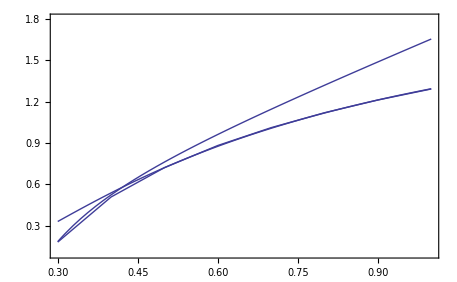

```mathematica
res[M2_]:=(12 π^2 m^2)/g^2 E^(-m^2/M2)/.{g->5.462404034434056,m->0.7643953151769755}
plotres1 = Plot[res[M2], {M2, min, max}];
Show[{plotsub, plotfull,plotres1}, PlotRange->{{min,max},{0.1,1.8}},
AxesOrigin->{0.2,0.3}, Frame->True, Axes->False]
```

### 有宽度基态

ρ介子质量实验值为m_ρ=0.77549±0.00034，宽度Γ=0.1491±0.0008，
m^2=0.601
耦合常数的实验值为(g_ρ^2/(4π))_exp≃2.3，即g2→28.9  or g→5.38 。
f = m^2/g^2=0.021。

#### 拟合质量、宽度和耦合常数

这里选定M2范围是[ 0.42,  1.30]

```mathematica
Clear[a, pts, plotsub, plotfull, f1, cont, contsubtract, s0]
Λ=0.1; s0=1.5; up=13;
minp = 0.43; maxp = 1.2; dM2 = 0.05;
smin=0.2; smax = 1.0;
a[M2_]:=(4π)/9 1/Log[M2/Λ^2]
f1[M2_]:=3/2 M2(1+a[M2]/π+0.1 (0.6/M2)^2-0.14(0.6/M2)^3)
cont[M2_]:=∫_s0^up 3/2(1+a[s]/π)E^(-s/M2)ⅆs//N
contsubtract[M2_]:=f1[M2]-cont[M2]

Timing[
ptswidrho = Table[contsubtract[M2],{M2, minp, maxp, dM2}] ;
]
datawidrho=Transpose[Join[{Range[minp, maxp, 0.05]}, {ptswidrho}]];
Timing[
FindFit[datawidrho, Re[∫_smin^smax 12π frho(Γ m)/((s-m^2)^2+Γ^2 m^2)E^(-s/M2)ⅆs] , {{Γ,0.1}, {m,0.7}, {frho,0.02}}, M2]
]
```

{26.489,Null}

{8.689,{Γ→-4.75328×10^-11,m→0.764554,frho→0.0195885}}

```mathematica
Clear[s0, f]
smin=0.; smax=1.5; 
FindFit[datawidrho,Re[∫_smin^smax 12π frho(Γ m)/((s-m^2)^2+Γ^2 m^2)E^(-s/M2)ⅆs]/.{Γ->0.15}, {m, frho}, M2]
```

{m→0.799094,frho→0.0227862}

### 零宽度基态和零宽度激发态

#### 考虑到激发态的贡献。

这里s0使用2.1。

{21.607,Null}

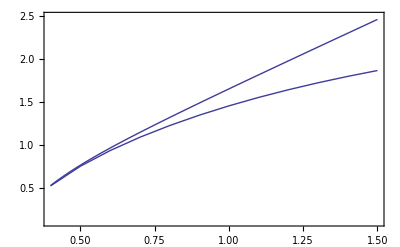

```mathematica
Clear[pts, plotsub, plotfull, cont, pts]
Λ=0.1; s0=2.1; up=13;
min =0.4; max=1.5;
a[M2_]:=(4π)/9 1/Log[M2/Λ^2]
f1[M2_]:=3/2 M2(1+a[M2]/π+0.1 (0.6/M2)^2-0.14(0.6/M2)^3)
f2[M2_]:=(3 M2^2)/2(1+a[M2]/π-0.1(0.6/M2)^2+0.28(0.6/M2)^3)
cont[M2_]:=∫_s0^up 3/2(1+a[s]/π)E^(-s/M2)ⅆs//N

contsubtract[M2_]:=f1[M2]-cont[M2]

Timing[
pts = Table[contsubtract[M2],{M2,min,max, 0.1}] ;
]

data = Transpose[Join[{Range[min, max, 0.1]}, {pts}]];
plotsub=ListLinePlot[data];
plotfull=Plot[f1[M2],{M2,min, max}];
Show[{plotsub, plotfull}, PlotRange->{{min,max},{0.1,2.5}},
AxesOrigin->{0.2,0.3}, Frame->True, Axes->False]
```

#### 确定合适的M^2的范围。

首先高阶修正小于总贡献的20%。

```mathematica
FindRoot[Abs[(0.1 (0.6/M2)^2-0.14(0.6/M2)^3)/(1+a[M2]/π+0.1 (0.6/M2)^2-0.14(0.6/M2)^3)]==0.2,{M2,1}]
```

{M2→0.429588}

其次连续谱贡献小于总贡献的20%。

```mathematica
Timing[
Table[cont[M2]/f1[M2],{M2, 1.2, 1.8, 0.1}]
]
```

{11.716,{0.170156,0.194861,0.218903,0.242134,0.264463,0.285835,0.306227}}

这里选定M2范围是[ 0.42,  1.30]

#### 拟合基态和激发态质量和耦合常数

ρ介子质量实验值为m_ρ=0.77549±0.00034，宽度Γ=0.1491±0.0008，
m^2=0.601
耦合常数的实验值为(g_ρ^2/(4π))_exp≃2.3，
即g2→28.9  or g→5.38 。

ρ介子激发态质量实验值为m_ρ'=1.465±0.025，宽度Γ=0.400±0.060。
mp^2→2.13

```mathematica
min1 = 0.5; max1 = 1.3; dM2=0.05;
Timing[
pts2 = Table[contsubtract[M2],{M2,min1,max1, dM2}];
]
data=Transpose[Join[{Range[min1, max1, dM2]}, {pts2}]];
FindFit[data,(12 π^2 m2)/g2 E^(-m2/M2)+(12 π^2 mprime2)/gprime2 E^(-mprime2/M2),{ g2, m2, gprime2, mprime2},M2]
{√m2 . √mprime2}/.%
```

{28.142,Null}

{g2→28.1017,m2→0.639354,gprime2→332.323,mprime2→3.66236}

{0.799596.1.91373}

#### 指定基态的质量和耦合常数

```mathematica
min1 = 0.5; max1 = 1.3; dM2=0.05;
Timing[
pts2 = Table[contsubtract[M2],{M2,min1,max1, dM2}];
]
data=Transpose[Join[{Range[min1, max1, dM2]}, {pts2}]];
FindFit[data,(12 π^2 m2)/g2 E^(-m2/M2)+(12 π^2 mprime2)/gprime2 E^(-mprime2/M2)/.{g2->28.9, m2->0.6},
{gprime2, mprime2}, M2]
{ √mprime2}/.%
```

{28.251,Null}

{gprime2→282.167,mprime2→2.11947}

{1.45584}

### 零宽度基态和有宽度激发态

s0为2.1，结果不好。
选s0为2.3。

观察s0的影响。

```mathematica
up=13;
cont[M2_, s0_]:=∫_s0^up 3/2(1+a[s]/π)E^(-s/M2)ⅆs//N
Table[cont[M2],{M2,0.9,1.2,0.1}, {s0,1.8,2.5,0.1}]
```

{{0.197358,0.176509,0.157867,0.141197,0.126291,0.112961,0.10104,0.0903787},{0.267733,0.242129,0.218979,0.198048,0.179121,0.162007,0.14653,0.132534},{0.346733,0.316441,0.288804,0.263586,0.240576,0.219578,0.200417,0.182931},{0.433348,0.3985,0.366465,0.337012,0.309932,0.285034,0.26214,0.241089}}

#### 考虑到激发态的贡献。

{21.248,Null}

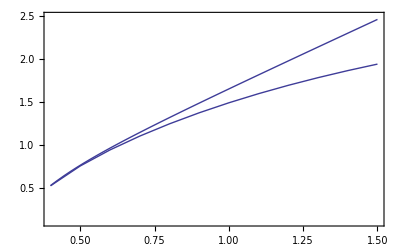

```mathematica
Clear[pts, plotsub, plotfull, cont, pts]
Λ=0.1; s0=2.3; up=13;
min =0.4; max=1.5;
a[M2_]:=(4π)/9 1/Log[M2/Λ^2]
f1[M2_]:=3/2 M2(1+a[M2]/π+0.1 (0.6/M2)^2-0.14(0.6/M2)^3)
f2[M2_]:=(3 M2^2)/2(1+a[M2]/π-0.1(0.6/M2)^2+0.28(0.6/M2)^3)
cont[M2_]:=∫_s0^up 3/2(1+a[s]/π)E^(-s/M2)ⅆs//N

contsubtract[M2_]:=f1[M2]-cont[M2]

Timing[
pts = Table[contsubtract[M2],{M2,min,max, 0.1}] ;
]

data = Transpose[Join[{Range[min, max, 0.1]}, {pts}]];
plotsub=ListLinePlot[data];
plotfull=Plot[f1[M2],{M2,min, max}];
Show[{plotsub, plotfull}, PlotRange->{{min,max},{0.1,2.5}},
AxesOrigin->{0.2,0.3}, Frame->True, Axes->False]
```

#### 确定合适的M^2的范围。

由于考虑到了激发态，所以要求连续谱贡献小于总贡献的20%。

首先高阶修正小于总贡献的20%。

```mathematica
FindRoot[Abs[(0.1 (0.6/M2)^2-0.14(0.6/M2)^3)/(1+a[M2]/π+0.1 (0.6/M2)^2-0.14(0.6/M2)^3)]==0.2,{M2,1}]
```

{M2→0.429588}

其次连续谱贡献小于总贡献的20%。

```mathematica
Timing[
Table[cont[M2]/f1[M2],{M2, 1.2, 1.5, 0.05}]
]
```

{11.7,{0.143913,0.155453,0.166934,0.178325,0.189602,0.200741,0.211726}}

这里选定M2范围是[ 0.42,  1.45]

#### 拟合基态和激发态质量和耦合常数

ρ介子质量实验值为m_ρ=0.77549±0.00034，宽度Γ=0.1491±0.0008，
m^2=0.601
耦合常数的实验值为(g_ρ^2/(4π))_exp≃2.3，
即g2→28.9  or g→5.38 。

ρ介子激发态质量实验值为m_ρ'=1.465±0.025，宽度Γ=0.400±0.060。
mp^2→2.13

```mathematica
Clear[pts2]
min1 = 0.43; max1 = 1.45; dM2=0.05;
smin=0.8; smax=2.2;
Timing[
pts2 = Table[contsubtract[M2],{M2,min1,max1, dM2}];
]
data = Transpose[Join[{Range[min1, max1, dM2]}, {pts2}]];
Timing[
FindFit[data,(12 π^2 m2)/g2 E^(-m2/M2)+Re[∫_smin^smax 12π frhop(Γ mprime)/((s-mprime^2)^2+Γ^2 mprime^2)E^(-s/M2)ⅆs],
	{m2, g2, {mprime,1.5}, frhop, {Γ,0.4}}, M2]
]
Timing[
FindFit[data,(12 π^2 m2)/g2 E^(-m2/M2)+Re[∫_smin^smax 12π frhop(Γ mprime)/((s-mprime^2)^2+Γ^2 mprime^2)E^(-s/M2)ⅆs]/.
	{g2->30, m2->0.6,mprime->1.46},
	{frhop, Γ}, M2]
]
Timing[
FindFit[data,(12 π^2 m2)/g2 E^(-m2/M2)+Re[∫_smin^smax 12π frhop(Γ mprime)/((s-mprime^2)^2+Γ^2 mprime^2)E^(-s/M2)ⅆs]/.
	{g2->30,m2->0.6,mprime->1.46, Γ->0.4},
	{frhop}, M2]
]
```

{35.006,Null}

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{12.091,{m2→0.556381,g2→33.3559,mprime→-7.75502,frhop→-3.3484,Γ→8.10411}}

{8.704,{frhop→0.019697,Γ→0.20406}}

{8.237,{frhop→0.0214318}}

```mathematica
Clear[pts2]
min1 = 0.43; max1 = 1.45; dM2=0.05;
smin=0.8; smax=2.2;
Timing[
pts2 = Table[contsubtract[M2],{M2,min1,max1, dM2}];
]
data = Transpose[Join[{Range[min1, max1, dM2]}, {pts2}]];
Timing[
FindFit[data,(12 π^2 m2)/g2 E^(-m2/M2)+Re[∫_smin^smax 12π frhop(Γ mprime)/((s-mprime^2)^2+Γ^2 mprime^2)E^(-s/M2)ⅆs]/.
	{g2->28.9, m2->0.6,Γ->0.4},
	{frhop, mprime}, M2]
]
Timing[
FindFit[data,(12 π^2 m2)/g2 E^(-m2/M2)+Re[∫_smin^smax 12π frhop(Γ mprime)/((s-mprime^2)^2+Γ^2 mprime^2)E^(-s/M2)ⅆs]/.
	{g2->28.9,m2->0.6,mprime->1.46, Γ->0.4},
	{frhop}, M2]
]
```

{35.459,Null}

{8.175,{frhop→0.0192439,mprime→1.49832}}

{8.252,{frhop→0.0165547}}

```mathematica
Clear[pts2]
min1 = 0.43; max1 = 1.3; dM2=0.05;
smin=0.8; smax=2.3;
Timing[
pts2 = Table[contsubtract[M2],{M2,min1,max1, dM2}];
]
data = Transpose[Join[{Range[min1, max1, dM2]}, {pts2}]];
Timing[
FindFit[data,(12 π^2 m2)/g2 E^(-m2/M2)+Re[∫_smin^smax 12π frhop(Γ mprime)/((s-mprime^2)^2+Γ^2 mprime^2)E^(-s/M2)ⅆs]/.
	{g2->30, m2->0.6, mprime->1.46},
	{frhop, Γ}, M2]
]
Timing[
FindFit[data,(12 π^2 m2)/g2 E^(-m2/M2)+Re[∫_smin^smax 12π frhop(Γ mprime)/((s-mprime^2)^2+Γ^2 mprime^2)E^(-s/M2)ⅆs]/.
	{g2->30, m2->0.6, mprime->1.46, Γ->0.4},
	{frhop}, M2]
]
```

{30.108,Null}

{8.409,{frhop→0.018345,Γ→0.279964}}

{8.252,{frhop→0.0196206}}

#### 画出基态和激发态的贡献（参数都用实验值）

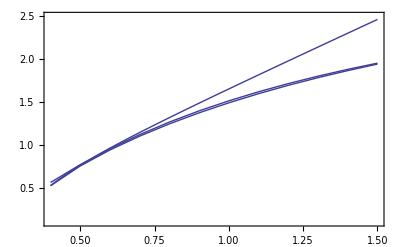

```mathematica
ptsGroundAndRes=Table[(12 π^2 m2)/g2 E^(-m2/M2)+Re[∫_smin^smax 12π frhop(Γ mprime)/((s-mprime^2)^2+Γ^2 mprime^2)E^(-s/M2)ⅆs]/.
{g2->29,m2->0.6,mprime->1.47,frhop->0.017, Γ->0.4},{M2,min, max, 0.1 }];
dataGroundAndRes=Transpose[Join[{Range[min, max, 0.1]}, {ptsGroundAndRes}]];
plotGroundAndRes=ListLinePlot[dataGroundAndRes];
Show[{plotsub, plotfull, plotGroundAndRes}, PlotRange->{{min,max},{0.1,2.5}},
AxesOrigin->{0.2,0.3}, Frame->True, Axes->False]
```

## π 介子

### 只考虑基态

#### 求出共振态贡献。

{17.815,Null}

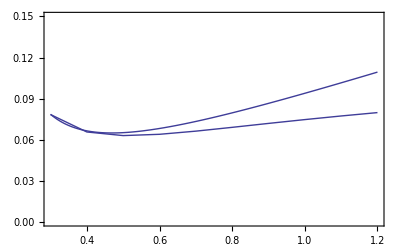

```mathematica
Clear[a, pts, plotsub, plotfull, contsubtract, cont, f1]
Λ=0.1; s0=1.5; up=13;
min =0.3; max=1.2;
a[M2_]:=(4π)/9 1/Log[M2/Λ^2]
f1[M2_]:=1/(4π)M2(1+a[M2]/π+0.1 (0.6/M2)^2+0.22(0.6/M2)^3)
cont[M2_]:=∫_s0^up 1/(4π)(1+a[s]/π)E^(-s/M2)ⅆs//N

contsubtract[M2_]:=f1[M2]-cont[M2]

Timing[
pts = Table[contsubtract[M2],{M2,min,max, 0.1}] ;
]

datapi=Transpose[Join[{Range[min, max, 0.1]}, {pts}]];
plotsub=ListLinePlot[datapi];
plotfull=Plot[f1[M2],{M2,min, max}];
Show[{plotsub, plotfull}, PlotRange->{{min,max},{0.,0.15}},
AxesOrigin->{0.,0.3}, Frame->True, Axes->False]
```

#### 确定合适的M^2的范围。

首先高阶修正小于总贡献的30%。

```mathematica
FindRoot[Abs[(0.1 (0.6/M2)^2+0.22(0.6/M2)^3)/(1+a[M2]/π+0.1 (0.6/M2)^2+0.22(0.6/M2)^3)]==0.3,{M2,1}]
```

{M2→0.51769}

其次连续谱贡献小于总贡献的30%。

```mathematica
Timing[
Table[cont[M2]/f1[M2],{M2, 0.8, 1.4, 0.1}]
]
```

{11.419,{0.132777,0.169148,0.204538,0.238364,0.270354,0.300418,0.328566}}

#### 拟合出π介子耦合常数和A_1介子质量和耦合常数。

f_π=0.133; 
m_A_1=1.23±0.04GeV
m_π'=1.30±0.10GeV
π(1800)

```mathematica
M2min=0.52; M2max=1.3; dM2=0.05;
Timing[
pts1 = Table[contsubtract[M2],{M2,M2min,M2max, dM2}] ;
]
datapi1=Transpose[Join[{Range[M2min, M2max, dM2]}, {pts1}]];
FindFit[datapi1,π fpi^2 + π mA2/gA2 E^(-mA2^2/M2), {fpi, mA2, gA2}, M2]
{fpi,√mA2,√gA2}/.%
```

{26.536,Null}

{fpi→0.138192,mA2→1.36953,gA2→45.3784}

{0.138192,1.17027,6.73635}

### 考虑π介子基态和激发态

{20.436,Null}

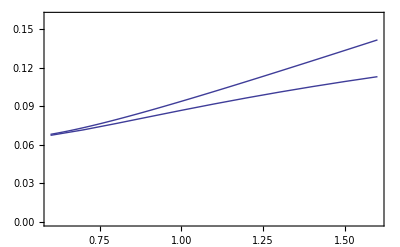

```mathematica
Clear[a, pts, plotsub, plotfull, contsubtract, cont, f1, s0]
Λ=0.1; s0=2.5; up=13;
min =0.6; max=1.6;
a[M2_]:=(4π)/9 1/Log[M2/Λ^2]
f1[M2_]:=1/(4π)M2(1+a[M2]/π+0.1 (0.6/M2)^2+0.22(0.6/M2)^3)
cont[M2_]:=∫_s0^up 1/(4π)(1+a[s]/π)E^(-s/M2)ⅆs//N

contsubtract[M2_]:=f1[M2]-cont[M2]

Timing[
pts = Table[contsubtract[M2],{M2,min,max, 0.1}] ;
]

datapi=Transpose[Join[{Range[min, max, 0.1]}, {pts}]];
plotsub=ListLinePlot[datapi];
plotfull=Plot[f1[M2],{M2,min, max}];
Show[{plotsub, plotfull}, PlotRange->{{min,max},{0.,0.16}},
AxesOrigin->{0.,0.3}, Frame->True, Axes->False]
```

#### 确定合适的M^2的范围。

首先高阶修正小于总贡献的30%。

```mathematica
FindRoot[Abs[(0.1 (0.6/M2)^2+0.22(0.6/M2)^3)/(1+a[M2]/π+0.1 (0.6/M2)^2+0.22(0.6/M2)^3)]==0.10,{M2,1.}]
```

{M2→0.863225}

其次连续谱贡献小于总贡献的30%。

```mathematica
Timing[
Table[cont[M2]/f1[M2],{M2, 1.0, 1.6, 0.1}]
]
```

{11.966,{0.0748763,0.0955746,0.116943,0.138556,0.160097,0.181334,0.202098}}

#### 拟合出π介子激发态耦合常数和A_1介子质量和耦合常数。

```mathematica
M2min=0.86; M2max=1.2; dM2=0.01;
Timing[
pts2 = Table[contsubtract[M2],{M2,M2min,M2max, dM2}] ;
]
datapi2=Transpose[Join[{Range[M2min, M2max, dM2]}, {pts2}]];
FindFit[datapi2,π fpi^2 +π fpiprime^2 E^(-mpiprime^2/M2)+ π mA2/gA2 E^(-mA2^2/M2), 
	{fpi, gA2, mA2, {fpiprime,1}, {mpiprime,1}}, M2]
{fpi,√gA2,√mA2, fpiprime, mpiprime}/.%
```

{60.278,Null}

{fpi→0.167643,gA2→42.4429,mA2→265.236,fpiprime→-111.375,mpiprime→-263.221}

{0.167643,6.51482,16.2861,-111.375,-263.221}

```mathematica
FindFit[datapi2,π fpi^2 +π fpiprime^2 E^(-mpiprime^2/M2)+ π mA2/gA2 E^(-mA2^2/M2)/.
{fpi->0.133, mA2->1.51}, {gA2, fpiprime, mpiprime}, M2]
```

{gA2→87.4051,fpiprime→0.188775,mpiprime→1.21227}